### From other notebooks

```mathematica
precompute[positions_,perturbedIndex_,s_,ν_, θ_]:= Block[
{
dp = Differences[positions],
betaList,
diffs,
reducedAngles
},
betaList =ArcTan@@@ Join[-dp[[1;;perturbedIndex-1]],dp[[perturbedIndex;;-1]]] ;
reducedAngles=θ +2 ArcCot[ⅇ^(-s+s ν)Cot[(betaList-θ)/2]];
reducedAngles=Insert[reducedAngles,θ,perturbedIndex];
Transpose@{Cos[reducedAngles],Sin[reducedAngles]}]
```

```mathematica
displacements[perturbedIndex_,positionList_,s_,ν_,θ_]:= 
Block[{newPositions,betaList,Δ  },
Δ=precompute[positionList,perturbedIndex,s,ν,θ];
newPositions[perturbedIndex] =positionList[[perturbedIndex]]+s AngleVector[θ];
newPositions[index_] := newPositions[index]=
Module[{nextIndex=index-Sign[index-perturbedIndex]},
newPositions[nextIndex] + Δ[[index]]
];
newPositions/@Range[Length[Δ]]
]
```

```mathematica
chainGraphic[positions_]:= 
{FaceForm[Orange],EdgeForm[Black],Disk[#,1/2]&/@(positions),
MapIndexed[Text[#2[[1]],#1]&,(positions)]}
```

## Work on newton’s method for removing overlap

#### An example that works almost immediately. Here the overlap is fairly simple. A more complicated case can be queried by using this initial state: positions=displacements[11,positions,.5,.1,0]; Really complicated from this positions=displacements[11,positions,1,.1,0]; But, I am not sure if there is a guaranteed that it will always work. Question is: Do the complicated cases really matter? It is unlikely that the algorithm is so bad that we would ever reach one. But, it is unsatisfying that the algorithm may never return in a bizarre side case.

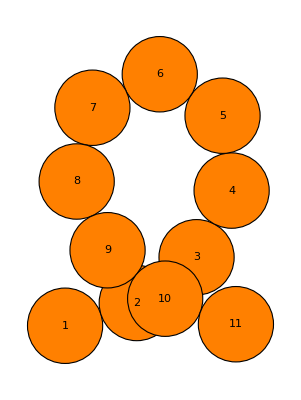

```mathematica
positions=AnglePath[ConstantArray[0.565,10]];
positions=displacements[11,positions,.7,.1,0];
nf= Nearest[positions->All];
Graphics[chainGraphic[positions]]
```

#### Neighbor finding with distance, collision checking

```mathematica
findNotNearestNeighborUpToDistance[positions_,nf_,whichParticle_,beyondNearstNeighbor_, distance_]:=Block[{nnn},
nnn=Select[Abs[#Index-whichParticle] >1 &][nf[positions[[whichParticle]],{beyondNearstNeighbor + 3,distance}]];
Which[
nnn!={},Join[<|"Me"-> whichParticle|>,#]&/@nnn,
True,{}
]
]
```

```mathematica
findAllNotNearestNeighborUpToDistance[positions_,nf_,beyondNearstNeighbor_, distance_]:=findNotNearestNeighborUpToDistance[positions,nf,#,beyondNearstNeighbor, distance]&/@Range[Length[positions]]
```

```mathematica
findAllNotNearestNeighborUpToDistance[positions,nf,13,1]
```

{{},{<|Me→2,Element→{-1.35711,0.376726},Index→10,Distance→0.382259|>,<|Me→2,Element→{-2.12351,1.01909},Index→9,Distance→0.800005|>},{<|Me→3,Element→{-1.35711,0.376726},Index→10,Distance→0.689741|>},{},{},{},{},{},{<|Me→9,Element→{-1.73509,0.319704},Index→2,Distance→0.800005|>},{<|Me→10,Element→{-1.73509,0.319704},Index→2,Distance→0.382259|>,<|Me→10,Element→{-0.939751,0.925865},Index→3,Distance→0.689741|>},{}}

```mathematica
countCollisions[positions_,nf_]:= Block[{numberOverlaps=0},
Do[
numberOverlaps = Length[
Select[
Abs[#Index-particleIndex]>1 &&#Distance < 1&][ nf[positions[[particleIndex]],13]]
];
If[numberOverlaps>0,Return[numberOverlaps]],
{particleIndex,1,Length[positions]}];
numberOverlaps

]
```

### Overlap force

```mathematica
force[pMe:{xMe_,yMe_},pOther:{xOther_,yOther_}]:= Block[{dp = pOther-pMe,magSq},
magSq= dp.dp;
(-dp (1-magSq))/(magSq)^4]
```

### Neighborhood is a result from findAllNotNearestNeighborUpToDistance

```mathematica
computeForceInNeighborhood[positions_,neighborhood_List]:=
Block[{ positionList,position,myIndex},
If[Length[neighborhood]==0,Return[<|"Force"->{0,0}|>]];
myIndex = neighborhood[[1,"Me"]];
positionList =neighborhood[[All,"Element"]];
position=positions[[myIndex]];
<|"Index"->myIndex,"Force"->Total[force[position,#]&/@positionList]|>
]
```

```mathematica
(*displacements[perturbedIndex_,positionList_,s_,ν_,θ_]*)
```

### relaxOverlaps: find overlapping neighborhoods: assumption is that is never called unless there are overlaps. Nearest function is passed to computeForceInNeighborhood Find all non-zero forces Use either the largest total force on a single particle to move it, or randomly select a force.

```mathematica
relaxOverlaps[positions_, nf_]:= Block[
{overlappingNeighborhoods,forces,largestForce,randomForce},
overlappingNeighborhoods=findAllNotNearestNeighborUpToDistance[positions,nf,13, 1];
forces =computeForceInNeighborhood[positions,#]&/@overlappingNeighborhoods;
(*Echo[forces];*)
forces =Select[#Force!={0,0}&][forces];
(*Echo[forces];*)
largestForce =First[MaximalBy[forces,Norm[#Force]&]];
(*Echo[largestForce,"largest force in relax"];*)
(*interesting, using the largest force tends to get stuck in a local minimum*)
randomForce = RandomChoice[forces];
(*Echo[largestForce];*)
displacements[randomForce["Index"],
positions,
Min[{Norm[randomForce["Force"]],0.01}] (*hack to limit how far a particle is pushed*),
0,
ArcTan@@randomForce["Force"]]
(*displacements[perturbedIndex_,positionList_,s_,ν_,θ_]*)
]
```

#### Testing

```mathematica
relaxedPositions= positions;
originalGraphic = Graphics[chainGraphic[relaxedPositions]];
nf =Nearest[relaxedPositions->All];
graphic= Graphics[chainGraphic[relaxedPositions]]
```

-Graphics-

```mathematica
relaxOverlaps[relaxedPositions,nf]
```

{{-2.69783,0.0147467},{-1.74498,0.31819},{-0.946756,0.920553},{-0.47327,1.80135},{-0.58405,2.7952},{-1.41547,3.35084},{-2.30994,2.90371},{-2.50994,1.92391},{-2.09052,1.01612},{-1.31933,0.37951},{-0.376821,0.0453272}}

```mathematica
Do[
If[Flatten[findAllNotNearestNeighborUpToDistance[relaxedPositions,nf,13,1]]=={} (*not the most efficient collision detector, use throw instead*),Break[]];
relaxedPositions =relaxOverlaps[relaxedPositions,nf];
nf =Nearest[relaxedPositions->All];
graphic = chainGraphic[relaxedPositions];
Pause[0.05]
,
{1000}
]
```

$Aborted

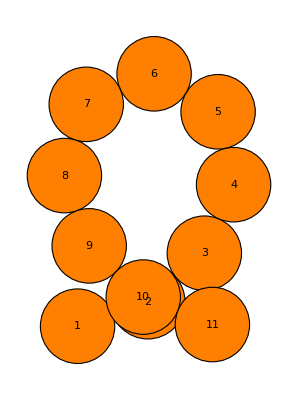

```mathematica
Row[{originalGraphic,Dynamic[Graphics[graphic]]}]
```

## New displacements function.

```mathematica
Clear[displacements]
```

```mathematica
Options[displacements]= {"Maximum Relaxation Attempts"-> 100};
displacements[perturbedIndex_,positionList_,s_,ν_,θ_, OptionsPattern[]]:= 
Block[{newPositions,betaList,Δ , displacedPositions, nf,
relaxationTries = 0, sReduced=s},
Δ=precompute[positionList,perturbedIndex,s,ν,θ];
newPositions[perturbedIndex] =positionList[[perturbedIndex]]+s AngleVector[θ];
newPositions[index_] := newPositions[index]=
Module[{nextIndex=index-Sign[index-perturbedIndex]},
newPositions[nextIndex] + Δ[[index]]
];
displacedPositions=newPositions/@Range[Length[Δ]];
nf = Nearest[displacedPositions->All];

If[countCollisions[displacedPositions,nf] == 0,
Return[displacedPositions]];

While[countCollisions[displacedPositions,nf] != 0 && ++relaxationTries < OptionValue["Maximum Relaxation Attempts"],
displacedPositions =relaxOverlaps[displacedPositions,nf];
nf =Nearest[displacedPositions->All]
];

If[countCollisions[displacedPositions,nf] == 0,
Return[displacedPositions]];

While[
countCollisions[displacedPositions,nf] !=  0 ||
!PossibleZeroQ[Round[(sReduced=0.9 sReduced),.001]] ,
displacedPositions=displacements[perturbedIndex,positionList,sReduced,ν,θ]
];
displacedPositions
]
```

## Testing motion without overlaps

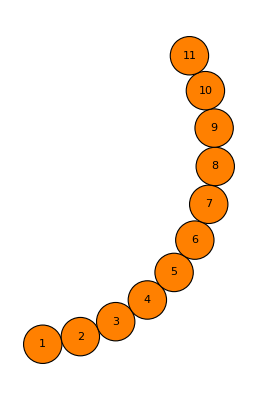

```mathematica
positions=AnglePath[ConstantArray[0.2,10]];
nf= Nearest[positions->All];
Graphics[chainGraphic[positions]]
```

```mathematica
currentGraphic = Graphics[chainGraphic[positions],PlotRange->15{{-1,1},{-1,1}},Frame->True];
Dynamic[currentGraphic]
```

```mathematica
With[{stiffness = 0, relativeTemperature = 0.1},
Do[
With[{whichParticle =RandomInteger[{1,Length[positions]}],
perturbation = RandomVariate[MaxwellDistribution[relativeTemperature]],
angle = RandomReal[2Pi]
},
(*positions =(Mean[positions]+#)&/@displacements[whichParticle,positions,perturbation,stiffness,angle];*)positions=displacements[whichParticle,positions,perturbation,stiffness,angle];
currentGraphic = Graphics[chainGraphic[positions],PlotRange->15{{-1,1},{-1,1}},Frame->True];
];Pause[0.05],
{1000}
]
]
```

$Aborted